## Set up equations for dipole trap potential

### Define rotations ( x-axis along symmetry axis of dipole trap )

```mathematica
r90x=RotationTransform[π/2,{1,0,0}];
r90y=RotationTransform[π/2,{0,1,0}];
r90z=RotationTransform[π/2,{0,0,1}];
r15z=RotationTransform[π/12,{0,0,1}];
rpz=RotationTransform[π/24,{0,0,1}]; (*plus*)
rmz=RotationTransform[-π/24,{0,0,1}];  (*minus*)

rplattz=RotationTransform[3 π/8,{0,0,1}]; (*plus*)
rmlattz=RotationTransform[-π/8,{0,0,1}];  (*minus*)
rtlatt=RotationTransform[π/2,{0,1,0}]; (*top-bot *)
```

Here I make a derivation of the numerical factor that gives the trap depth in uK

U= (ℏ Γ^2)/4[1/(ω_0+ω)+1/(ω_0-ω)] I/I_sat
  =(ℏ Γ^2)/4 1/(2 π c)[1/(1/λ_0+1/λ)+1/(1/λ_0-1/λ)] 1/I_sat(2 P)/(π w_0^2)

 
(ℏ Γ^2)/4 = 1/(2 π)48 uK/MHz(2 π 5.9 MHz)^2/4 = 2 π (417.72 uK) MHz = 2624.612 uK MHz

Isat =(hν Γ)/σ_0= (hν Γ)/(6 π (λ/(2π))^2)=(2π)/3(hν Γ)/λ^2=(2π)/3(hc Γ)/λ^3 = (2 π)/3 ((1.986 10^-25 J m )(2 π 5.9 MHz))/((670.9 10^-9 m)^3)=
= (4 π^2)/3((1.986^ J m )(5.9 Hz))/(670.9 m)^3 10^8 =51.0733 W/m^2 = 5.10733 mW/cm^2   = 51.0733  10^-12 W/um^2

1/(2 π c) = 5.30884 10^-10 1/(um MHz)


for λ=1070nm
[1/(1/λ_0+1/λ)+1/(1/λ_0-1/λ)]=2211.59 nm=2.21159 um

U =  2 π (417.72 uK MHz)( 5.30884 10^-10 1/(um MHz))[2.211590 um] 1/(51.0733 10^-12 W/um^2) (2 P)/(π w_0^2)

U =  38411 P/w_0^2

### Define trap geometry, depth is in units of uK. fcpow specifies trap depth fraction at end of evap.

```mathematica
(*Single beam without back reflection*)
(*P in Watts,w0, and all lengths in microns,*)
(*usingle propagates along r[[1]]*)
U0[λ_]:=If[λ==1.070, -38411/1.,If[λ==0.532,39561/1.0,ERROR],ERROR]
uone[λ_,P_,r_,w0_]:=U0[λ] P/w0^2( 1/(1+r[[1]]^2/((π w0^2/λ)^2)) Exp[-2(r[[2]]^2/w0^2+r[[3]]^2/w0^2)/(1+r[[1]]^2/((π w0^2/λ)^2))]);
uodt[P_,r_,w0_]:=uone[1.070,P[[1]],rpz[r],w0[[1]]]+uone[1.070,P[[2]],rmz[r]+{0,0,0},w0[[2]]];

(*The latest waists and powers are used here*)

(*Dec 10, 2012*)
w1=55.;
w2=55.;

(*Week of Jan 11, 2013*)
P1=38.;
P2=38.;


odt[fcpow_,r_]:=uodt[{(fcpow /10.)P1,(fcpow/10.)P2},r,{w1,w2}];
```

### Define functions for easy plotting

```mathematica
NicePlot1d[fun_,yrange_,range_]:=Module[
{plotpoints=80},
Plot[fun,{x,-range,range},PlotPoints->plotpoints,PlotRange->yrange,GridLines->Automatic,Frame->True,FrameLabel->{"μm","μK"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400}]
]
NicePlot[ fun_,ymin_,ymax_,range_]:=Module[
{plotpoints=80
},
DensityPlot[ fun, {x,-range,range},{y,-range,range},PlotPoints->plotpoints,PlotRange->{ymin,ymax},ColorFunctionScaling->True,ColorFunction->"AvocadoColors",FrameLabel->{"μm","μm"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400}]]
```

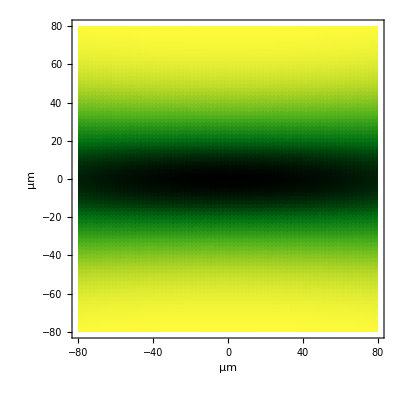

```mathematica
NicePlot[ odt[0.1,{x,y,0}],-100,100,80]
```

## Calculate trap depth and trap frequencies

### For the trap frequency simply make a series expansion

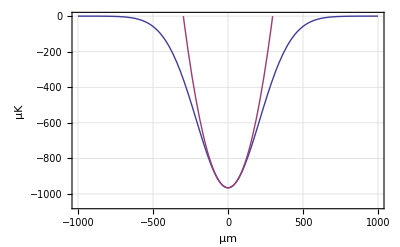
{-Graphics-,873.82}

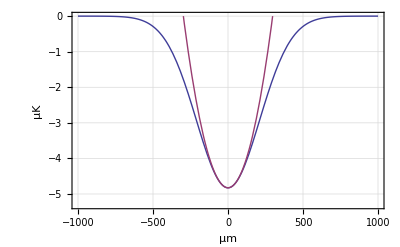
{-Graphics-,61.7884}

```mathematica
AxialTrapFreq[fcpow_]:=Module[{k,V0,f},
V0=SeriesCoefficient[ odt[fcpow,{x,y,z}], {x,0,0}]/.{y->0,z->0};
k=SeriesCoefficient[ odt[fcpow,{x,y,z}], {x,0,2}]/.{y->0,z->0}; (*uK/(um^2)*)
kbOverM6Li = 13.85 10^8;(*um^2/s^2/uK*)
f = 1/(2 π)√(2k kbOverM6Li);(*Hz*)
g=NicePlot1d[ {odt[fcpow,{x,0,0}],V0+k x^2},{1.1 V0,0},1000];
{g,f}
]
AxialTrapFreq[10.]
AxialTrapFreq[0.05]
```

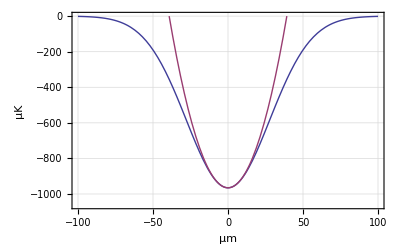
{-Graphics-,6633.65}

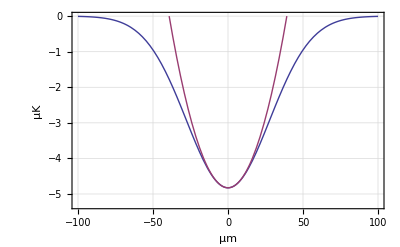
{-Graphics-,469.07}

```mathematica
RadialTrapFreq[fcpow_]:=Module[{k,V0,f},
V0=SeriesCoefficient[ odt[fcpow,{x,y,z}], {y,0,0}]/.{x->0,z->0};
k=SeriesCoefficient[ odt[fcpow,{x,y,z}], {y,0,2}]/.{x->0,z->0}; (*uK/(um^2)*)
kbOverM6Li = 13.85 10^8;(*um^2/s^2/uK*)
f = 1/(2 π)√(2k kbOverM6Li);(*Hz*)
g=NicePlot1d[ {odt[fcpow,{0,x,0}],V0+k x^2},{1.1 V0,0},100];
{g,f}
]
RadialTrapFreq[10.]
RadialTrapFreq[0.05]
```

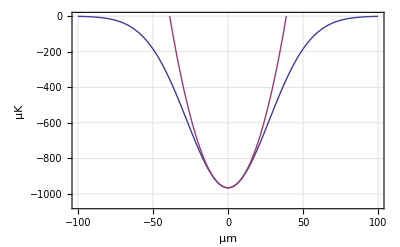
{-Graphics-,6690.9}

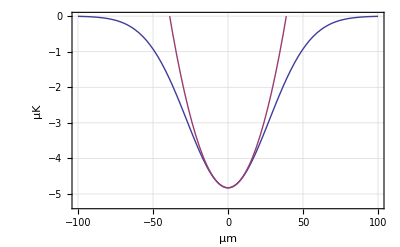
{-Graphics-,473.118}

```mathematica
RadialTrapFreqZ[fcpow_]:=Module[{k,V0,f},
V0=SeriesCoefficient[ odt[fcpow,{x,y,z}], {z,0,0}]/.{x->0,y->0};
k=SeriesCoefficient[ odt[fcpow,{x,y,z}], {z,0,2}]/.{x->0,y->0}; (*uK/(um^2)*)
kbOverM6Li = 13.85 10^8;(*um^2/s^2/uK*)
f = 1/(2 π)√(2k kbOverM6Li);(*Hz*)
g=NicePlot1d[ {odt[fcpow,{0,0,x}],V0+k x^2},{1.1 V0,0},100];
{g,f}
]
RadialTrapFreqZ[10.]
RadialTrapFreqZ[0.05]
```

### Define a function that produces all three trap frequencies

```mathematica
TrapFreqs[fcpow_]:=Module[{},
{AxialTrapFreq[fcpow][[2]],RadialTrapFreq[fcpow][[2]],RadialTrapFreqZ[fcpow][[2]]}
]
```

```mathematica
TrapFreqs[10.]
TrapFreqs[0.05]
```

{873.82,6633.65,6690.9}

{61.7884,469.07,473.118}

### For the trap depth we consider the depth of one beam only

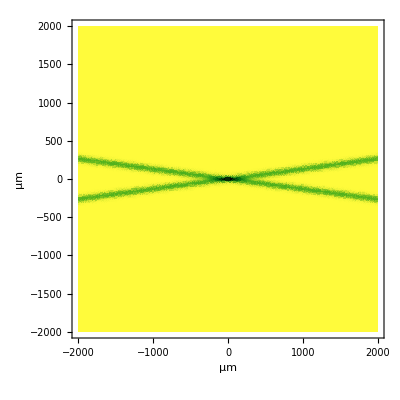

```mathematica
NicePlot[ odt[10.,{x,y,0}],-950,10,2000]
```

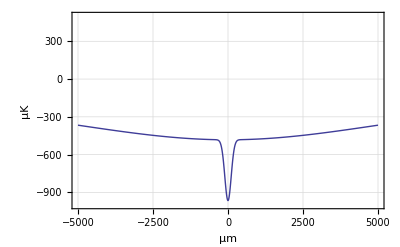

488.559

```mathematica
NicePlot1d[odt[10.,rpz[{x,0,0}]],{-1000,500},5000]

TrapDepth[fcpow_]:=Module[{beam,cross},
beam =odt[fcpow, rpz[{x,0,0}]]/.x->1000;
cross=odt[fcpow, {0.,0.,0.}];
beam-cross
]
TrapDepth[10.]
```

### Now define a function that tabulates trap depths and frequencies as a function of fcpow

```mathematica
odtnumbers[fcpow_]:=Module[{},
f=TrapFreqs[fcpow];
d=TrapDepth[fcpow];
Join[ {fcpow},{d},f]
]
odtnumbers[10.0]
```

{10.,488.559,873.82,6633.65,6690.9}

```mathematica
Module[{head,stream,dat},
dat=Table[ odtnumbers[fcpow],{fcpow,0.,11.,0.02}];
SetDirectory[NotebookDirectory[]];
head="#fcpow\tdepth(uK)\tfreqAx(Hz)\tfreqRd(Hz)\tfreqRdZ(Hz)\n";
stream=OpenWrite["odt.dat"];
WriteString[stream,head<>ExportString[dat,"Table"]];
Close[stream];]
```